# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",GenericModel->"Lorentz",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{2,2}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

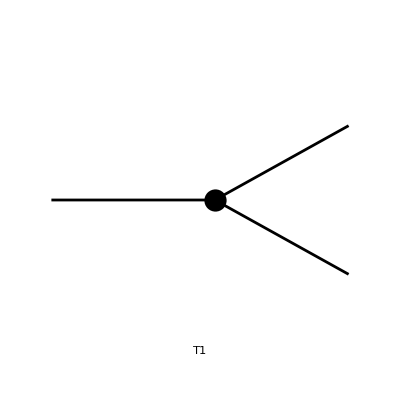

```mathematica
topsBorn=CreateTopologies[0,1->2,Adjacencies->3];
Paint[topsBorn];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

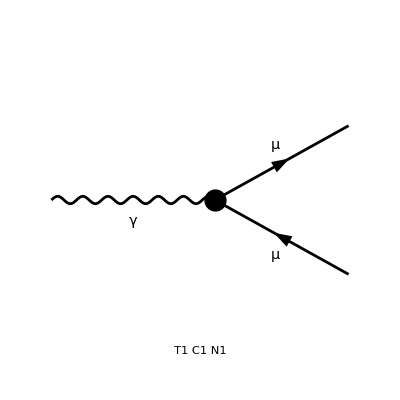

```mathematica
insBorn=InsertFields[topsBorn, process,QEDOnly];
Paint[insBorn];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
ampBorn=CalcFeynAmp[CreateFeynAmp[insBorn,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-26.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL Mat[F2]-EL Mat[F4]]

## Squared Matrix Element

```mathematica
_Hel=0;
```

```mathematica
smBorn=SquaredME[ampBorn]//Simplify;
smBorn=smBorn/.HelicityME[smBorn];
smBorn=PolarizationSum[smBorn]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-3.frm

running FORM...

ok

Alfa MM2 π (8-8 Pair3 Hel[2] Hel[3])

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

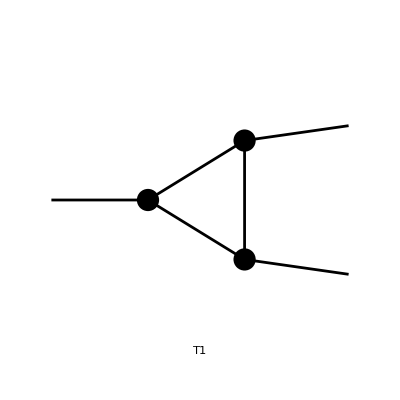

```mathematica
tops1Loop=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Reducible];
Paint[tops1Loop];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

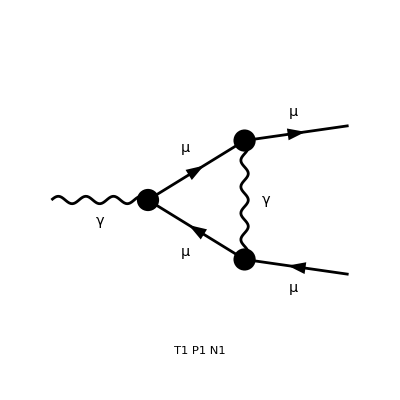

```mathematica
ins1Loop=InsertFields[tops1Loop, process,QEDOnly];
Paint[ins1Loop, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1Loop=CalcFeynAmp[CreateFeynAmp[ins1Loop,AmplitudeLevel->{Particles}],FermionChains -> Chiral];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-26.frm

running FORM...

ok

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1Loop=SquaredME[amp1Loop,ampBorn]//Simplify;
sm1Loop=sm1Loop/.HelicityME[sm1Loop];
sm1Loop=PolarizationSum[sm1Loop]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-26.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

-Alfa2 MM2 (2 Sub2+8 MM2 Sub3-2 (Pair2 Sub2+2 Abb34 Sub3) Hel[2] Hel[3])

```mathematica
UVDivergentPart[sm1Loop]
```

0

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#],FermionChains->Chiral]&,amp]/.amp[[0]]->List
```

## CounterTerms

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

> Top. 2 ad/bdce/ed.m, 0 diagrams

> Top. 3 ad/becd/ed.m, 0 diagrams

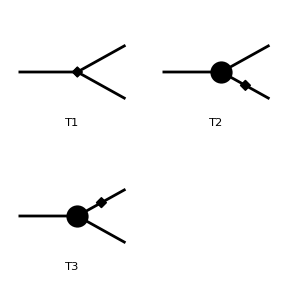

```mathematica
tops1CT=CreateCTTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->TadpoleCTs];
tops1CT=Delete[tops1CT,4];
Paint[tops1CT];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 3 Generic, 3 Classes, 3 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

> Top. 2 ad/bdce/ed.m, 0 diagrams

> Top. 3 ad/becd/ed.m, 0 diagrams

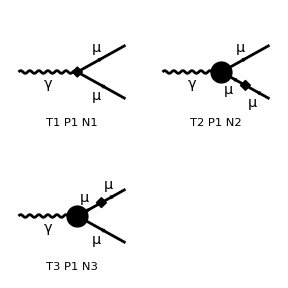

```mathematica
ins1CT=InsertFields[tops1CT, process,QEDOnly];
Paint[ins1CT, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1CT=CalcFeynAmp[CreateFeynAmp[ins1CT,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][EL (Sub13/4-1/2 Sub11 Den[MM2,MM2]) Mat[F2]-1/2 EL (Sub12+Sub10 Den[MM2,MM2]) Mat[F4]]

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1CT=SquaredME[amp1CT,ampBorn]//Simplify;
sm1CT=sm1CT/.HelicityME[sm1CT];
sm1CT=PolarizationSum[sm1CT]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

Alfa π (MM2 (Sub41+2 Sub51)-Abb39 MM (Sub41-2 Sub51) Hel[2]+Abb43 MM (Sub41-2 Sub51) Hel[3]+1/2 (Abb41 Sub41-2 Abb42 Sub51) Hel[2] Hel[3])

## CounterTerms List

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1CTList=calcFeynAmpList[CreateFeynAmp[ins1CT]]
```

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 2: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 3: 1 Generic, 1 Classes, 1 Particles amplitudes

in total: 3 Generic, 3 Classes, 3 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/4 EL Sub13 Mat[F2]-1/2 EL Sub12 Mat[F4]],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/2 EL Sub15 Den[MM2,MM2] Mat[F2]-1/2 EL Sub14 Den[MM2,MM2] Mat[F4]],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/2 EL Sub17 Den[MM2,MM2] Mat[F2]-1/2 EL Sub16 Den[MM2,MM2] Mat[F4]]}

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1CTList=Map[SquaredME[#,ampBorn]&,amp1CTList]//Simplify;
sm1CTList=Map[(#/.HelicityME[#])&,sm1CTList];
sm1CTList=Map[PolarizationSum[#]&,sm1CTList]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

{Alfa π (MM2 (Sub19+2 Sub20)-Abb39 MM (Sub19-2 Sub20) Hel[2]+Abb43 MM (Sub19-2 Sub20) Hel[3]+1/2 (Abb41 Sub19-2 Abb42 Sub20) Hel[2] Hel[3]),-16 Alfa MM MM2 π dMf1[2,2]^* Den[MM2,MM2] (-1+Pair2 Hel[2] Hel[3]),Alfa MM π dMf1[2,2]^* Den[MM2,MM2] (16 MM2+4 (Abb41-Abb42) Hel[2] Hel[3])}

```mathematica
df1=dMf1[2,2]/.CalcRenConst[sm1CTList[[2]]][[1,1]]
```

dMf1[2,2]

1/π Alfa MM (Finite/(4 CW2)-Re[B0i[bb0,MM2,0,MM2]]+(1/16 MM2 Re[B0i[bb0,MM2,MH2,MM2]]-((CW2 MM2-MW2 (8 SW2-16 SW2^2)) Re[B0i[bb0,MM2,MM2,MZ2]])/(16 CW2))/(MW2 SW2))+MM (-(Alfa Finite)/(8 CW2 π)-(Alfa Finite (1+2 CW2-(4-4 CW2) SW2+4 SW2^2))/(32 CW2 π SW2)-(Alfa (MM2+2 MW2) Re[B0i[bb1,MM2,0,MW2]])/(16 MW2 π SW2)-(Alfa Re[B0i[bb1,MM2,MM2,0]])/(2 π)-(Alfa MM2 Re[B0i[bb1,MM2,MM2,MH2]])/(16 MW2 π SW2)-(Alfa (CW2 MM2+MW2-4 MW2 SW2+8 MW2 SW2^2) Re[B0i[bb1,MM2,MM2,MZ2]])/(16 CW2 MW2 π SW2))

```mathematica
df2=dMf1[2,2]/.CalcRenConst[sm1CTList[[3]]][[1,1]]
```

dMf1[2,2]

1/π Alfa MM (Finite/(4 CW2)-Re[B0i[bb0,MM2,0,MM2]]+(1/16 MM2 Re[B0i[bb0,MM2,MH2,MM2]]-((CW2 MM2-MW2 (8 SW2-16 SW2^2)) Re[B0i[bb0,MM2,MM2,MZ2]])/(16 CW2))/(MW2 SW2))+MM (-(Alfa Finite)/(8 CW2 π)-(Alfa Finite (1+2 CW2-(4-4 CW2) SW2+4 SW2^2))/(32 CW2 π SW2)-(Alfa (MM2+2 MW2) Re[B0i[bb1,MM2,0,MW2]])/(16 MW2 π SW2)-(Alfa Re[B0i[bb1,MM2,MM2,0]])/(2 π)-(Alfa MM2 Re[B0i[bb1,MM2,MM2,MH2]])/(16 MW2 π SW2)-(Alfa (CW2 MM2+MW2-4 MW2 SW2+8 MW2 SW2^2) Re[B0i[bb1,MM2,MM2,MZ2]])/(16 CW2 MW2 π SW2))

## Results

```mathematica
smBorn
```

8 Alfa MM2 π

```mathematica
sm1Loop
```

-2 Alfa2 MM2 (Sub2+4 MM2 Sub3)

```mathematica
sm1LoopUV=UVDivergentPart[sm1Loop]
```

0

```mathematica
sm1CTUVList=Map[UVDivergentPart,sm1CTList]//Simplify
```

{0,-16 Alfa MM MM2 π dMf1[2,2]^* Den[MM2,MM2] (-1+Removed[Pair3] Hel[2] Hel[3]),Alfa MM π dMf1[2,2]^* Den[MM2,MM2] (16 MM2+4 (-Removed[Abb39]+Removed[Abb40]) Hel[2] Hel[3])}

```mathematica
UVDivergentPart[df1]+UVDivergentPart[df2]//Simplify
```

(Alfa Divergence MM (3 CW2 MM2+MW2+2 CW2 MW2+12 MW2 SW2-24 CW2 MW2 SW2-24 MW2 SW2^2))/(16 CW2 MW2 π SW2)

## One-Loop - Z Boson

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 8 Classes, 8 Particles insertions

in total: 6 Generic, 8 Classes, 8 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

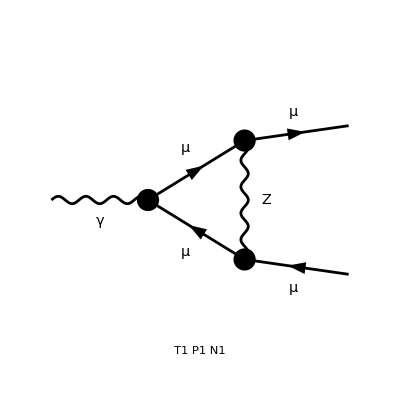

```mathematica
ins1LoopZ=InsertFields[tops1Loop, process];
ins1LoopZ=DiagramSelect[ins1LoopZ, !FreeQ[#,V[2]]&];
Paint[ins1LoopZ, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1LoopZ=CalcFeynAmp[CreateFeynAmp[ins1LoopZ,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/(CW2 π)Alfa EL MM Pair1 (1/4 (Sub21 C0i[cc12,0,MM2,MM2,MM2,MM2,MZ2]+Sub111 (1-2 SW2) C0i[cc2,0,MM2,MM2,MM2,MM2,MZ2])-SW2 C0i[cc22,0,MM2,MM2,MM2,MM2,MZ2]) Mat[F1]+1/(CW2 π)Alfa EL (((1-2 SW2)^2 (Finite/16-1/8 B0i[bb0,MM2,MM2,MZ2]+1/4 C0i[cc00,0,MM2,MM2,MM2,MM2,MZ2]))/SW2+1/8 MM2 Sub31 C0i[cc2,0,MM2,MM2,MM2,MM2,MZ2]) Mat[F2]+1/π Alfa EL MM Pair1 (-C0i[cc2,0,MM2,MM2,MM2,MM2,MZ2]+(Sub21 C0i[cc12,0,MM2,MM2,MM2,MM2,MZ2]+((1-2 SW2)^2 C0i[cc22,0,MM2,MM2,MM2,MM2,MZ2])/SW2)/(4 CW2)) Mat[F3]+1/(CW2 π)Alfa EL (SW2 (Finite/4-1/2 B0i[bb0,MM2,MM2,MZ2]+C0i[cc00,0,MM2,MM2,MM2,MM2,MZ2])+1/8 MM2 Sub31 C0i[cc2,0,MM2,MM2,MM2,MM2,MZ2]) Mat[F4]]

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1LoopZ=SquaredME[amp1LoopZ,ampBorn]//Simplify;
sm1LoopZ=sm1LoopZ/.HelicityME[sm1LoopZ];
sm1LoopZ=PolarizationSum[sm1LoopZ]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

1/(8 CW2)Alfa2 (-8 MM2^2 (Sub61-CW2 Sub91)-2 Abb39 MM (2 Sub112+Sub71) Hel[2]+(2 Abb43 MM (2 Sub112+Sub71)+(2 Abb42 Sub112+Abb41 Sub71) Hel[2]) Hel[3]-2 MM2 (2 Sub112-Sub71+2 (-Abb45 Sub61+Abb44 CW2 Sub91) Hel[2] Hel[3]+2 MM (Sub61+CW2 Sub91) (Pair3 Hel[2]+Pair4 Hel[3])))

```mathematica
UVDivergentPart[sm1LoopZ]
```

{0,{FF[Removed[F1]]→0,FF[Removed[F2]]→0,FFC[F1]→0,FFC[F2]→-(Alfa Divergence EL (1-2 SW2)^2)/(16 CW2 π SW2),FFC[F3]→0,FFC[F4]→-(Alfa Divergence EL SW2)/(4 CW2 π)}}

## One-Loop - W Boson

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 8 Classes, 8 Particles insertions

in total: 6 Generic, 8 Classes, 8 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

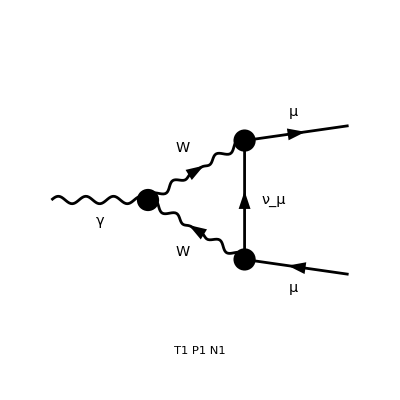

```mathematica
ins1LoopW=InsertFields[tops1Loop, process];
ins1LoopW=DiagramSelect[ins1LoopW,!FreeQ[#,V[3]]&& FreeQ[#,S]&];
Paint[ins1LoopW, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1LoopW=CalcFeynAmp[CreateFeynAmp[ins1LoopW,AmplitudeLevel->{Particles}],FermionChains -> Chiral];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

```mathematica
amp1LoopWList=Map[CalcFeynAmp[CreateFeynAmp[ins1LoopW[[0]][#],AmplitudeLevel->{Particles}],FermionChains -> Chiral]&,ins1LoopW];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1LoopW=SquaredME[amp1LoopW,ampBorn]//Simplify;
sm1LoopW=sm1LoopW/.HelicityME[sm1LoopW];
sm1LoopW=PolarizationSum[sm1LoopW]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-27.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-27.frm

running FORM...

ok

-1/(4 SW2)Alfa2 (MM2^2 (4 Sub131-6 Sub141-4 Sub171)-2 Abb39 MM Sub151 Hel[2]+Sub151 (2 Abb43 MM+Abb41 Hel[2]) Hel[3]+MM2 (2 Sub151+(-2 Abb45 Sub131+3 Abb42 Sub141+2 Abb44 Sub171) Hel[2] Hel[3]+2 MM (-3 Abb39 Sub141 Hel[2]+Pair3 (Sub131+Sub171) Hel[2]+(3 Abb43 Sub141+Pair4 (Sub131+Sub171)) Hel[3])))

```mathematica
UVDivergentPart[sm1LoopW]
```

0